```mathematica
Quantum Harmonic Oscillator
```

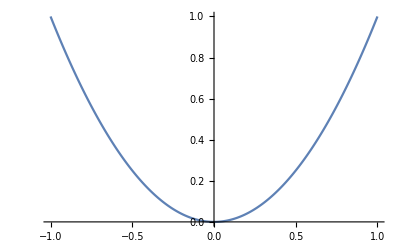

```mathematica
min=-1;max=1;step=500;
d=(max-min)/step;
V=Table[x^2,{x,Range[min,max,d]}];
ListLinePlot[V,PlotRange->All,DataRange->{min,max}]
```

```mathematica
f[En_]:=2(V-En);
```

```mathematica
u=ConstantArray[0,step];
g=ConstantArray[0,step];
u[[1]]=0;(*boundary conditions*)
g[[1]]=u[[1]](1-(d^2 f[Eni][[1]])/12);
u[[2]]=1;(*boundary conditions*)
g[[2]]=u[[2]](1-(d^2 f[Eni][[2]])/12);
(*g[[step]]=u[[step]](1-(d^2 f[[step]])/12);*)
u1=u;g=g1;
```

```mathematica
uend=0;
δ:=u[[step]]-uend;
δ1:=u1[[step]]-uend;
```

```mathematica
tail[En_]:=Do[g[[i+1]]=2 g[[i]]-g[[i-1]]+d^2 f[En][[i]]u[[i]];u[[i+1]]=g[[i+1]]/(1-(d^2 f[En][[i+1]])/12),{i,2,step-1,1}];
tail1[En_]:=Do[g1[[i+1]]=2 g1[[i]]-g1[[i-1]]+d^2 f[En][[i]]u1[[i]];u1[[i+1]]=g1[[i+1]]/(1-(d^2 f[En][[i+1]])/12),{i,2,step-1,1}];
```

```mathematica
For[En=0.1,δ δ1≥0,En+=0.0001,tail[En];tail1[En+0.0001]];
```